```mathematica
Quit[]
```

### non-attractor

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,H>0,k>0,xe>0,xs>0,-3<β<-3/2,1>f>0, BesselJ[1/2+β,xs]∈Reals, BesselJ[3/2+β,xs]∈Reals,BesselJ[-5/2-β,xs]∈Reals,BesselJ[-3/2-β,xs]∈Reals,BesselJ[-1/2-β,xs]∈Reals};
```

```mathematica
ζkSR1form1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1form2[τ_,k_]=(-I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(I k τ)(1-I k τ);
ζkSR1formp1[τ_,k_]=D[ζkSR1form1[τ,k], τ]//Simplify
ζkSR1formp2[τ_,k_]=D[ζkSR1form2[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSR1[τ_,k_]={{ζkSR1form1[τ,k]},{ζkSR1formp1[τ,k]}};
```

```mathematica
MSR1[τ_,k_]={{ζkSR1form1[τ,k],ζkSR1form2[τ,k]},{ζkSR1formp1[τ,k],ζkSR1formp2[τ,k]}};
```

```mathematica
ζkCRform1[τ_,k_,β_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-β Sqrt[-k τ]HankelH1[-3/2-β,-k τ];
ζkCRformp1[τ_,k_,β_]=D[ζkCRform1[τ,k,β], τ]//Simplify
ζkCRform2[τ_,k_,β_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-β Sqrt[-k τ]HankelH2[-3/2-β,-k τ];
ζkCRformp2[τ_,k_,β_]=D[ζkCRform2[τ,k,β], τ]//Simplify
```

-(H k τ (τs/τ)^-β (k τ HankelH1[-5/2-β,-k τ]-(3+2 β) HankelH1[-3/2-β,-k τ]-k τ HankelH1[-1/2-β,-k τ]))/(2 √2 √(-k ϵSR τ))

-(H k τ (τs/τ)^-β (k τ HankelH2[-5/2-β,-k τ]-(3+2 β) HankelH2[-3/2-β,-k τ]-k τ HankelH2[-1/2-β,-k τ]))/(2 √2 √(-k ϵSR τ))

```mathematica
MCR[τ_,k_,β_]={{ζkCRform1[τ,k,β],ζkCRform2[τ,k,β]},{ζkCRformp1[τ,k,β],ζkCRformp2[τ,k,β]}};
```

```mathematica
ζkSR2form1[τ_,k_,β_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-β 1/k^(3/2)E^(-I k τ)(1+I k τ)//Simplify;
ζkSR2formp1[τ_,k_,β_]=D[ζkSR2form1[τ,k,β], τ]//Simplify
ζkSR2form2[τ_,k_,β_]=(-I H)/(2Sqrt[ϵSR])(τs/τe)^-β 1/k^(3/2)E^(I k τ)(1-I k τ)//Simplify;
ζkSR2formp2[τ_,k_,β_]=D[ζkSR2form2[τ,k,β], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ (τs/τe)^-β

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ (τs/τe)^-β

```mathematica
MSR2[τ_,k_,β_]={{ζkSR2form1[τ,k,β],ζkSR2form2[τ,k,β]},{ζkSR2formp1[τ,k,β],ζkSR2formp2[τ,k,β]}};
```

```mathematica
ζkSR2[k_,β_]=Normal[Series[MSR2[τ,k,β].Inverse[MSR2[τe,k,β]].MCR[τe,k,β].Inverse[MCR[τs,k,β]].ζkSR1[τs,k],{τ,0,0}]][[1,1]];
```

```mathematica
sqrtcalPζSR2[xs_,β_,f_]=k^(3/2)/(Sqrt[2]π)ζkSR2[k,β]/.{k->-xs/τs,τe->f τs}//Simplify;
```

```mathematica
sqrtcalPζSR2[xs,β,f]
```

-((ⅇ^(ⅈ (1+f) xs) f^(-3/2+β) H ((1-ⅈ xs) ((-2 ⅇ^(-2 ⅈ f xs) (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 HankelH1[-3/2-β,f xs]-ⅈ (ⅈ+f xs+ⅇ^(-2 ⅈ f xs) (-ⅈ+f xs)) (f xs HankelH1[-5/2-β,f xs]+(3+2 β) HankelH1[-3/2-β,f xs]-f xs HankelH1[-1/2-β,f xs])) (xs HankelH2[-5/2-β,xs]+(3+2 β) HankelH2[-3/2-β,xs]-xs HankelH2[-1/2-β,xs])+ⅇ^(-2 ⅈ f xs) (xs HankelH1[-5/2-β,xs]+(3+2 β) HankelH1[-3/2-β,xs]-xs HankelH1[-1/2-β,xs]) (2 (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 HankelH2[-3/2-β,f xs]+(1+ⅈ f xs+ⅇ^(2 ⅈ f xs) (-1+ⅈ f xs)) (f xs HankelH2[-5/2-β,f xs]+(3+2 β) HankelH2[-3/2-β,f xs]-f xs HankelH2[-1/2-β,f xs])))+2 xs^2 (ⅇ^(-2 ⅈ f xs) (2 (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 HankelH1[-3/2-β,f xs]+(1+ⅈ f xs+ⅇ^(2 ⅈ f xs) (-1+ⅈ f xs)) (f xs HankelH1[-5/2-β,f xs]+(3+2 β) HankelH1[-3/2-β,f xs]-f xs HankelH1[-1/2-β,f xs])) HankelH2[-3/2-β,xs]+HankelH1[-3/2-β,xs] (-2 ⅇ^(-2 ⅈ f xs) (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 HankelH2[-3/2-β,f xs]-ⅈ (ⅈ+f xs+ⅇ^(-2 ⅈ f xs) (-ⅈ+f xs)) (f xs HankelH2[-5/2-β,f xs]+(3+2 β) HankelH2[-3/2-β,f xs]-f xs HankelH2[-1/2-β,f xs])))))/(8 √2 π xs^4 √ϵSR ((-HankelH1[-5/2-β,xs]+HankelH1[-1/2-β,xs]) HankelH2[-3/2-β,xs]+HankelH1[-3/2-β,xs] (HankelH2[-5/2-β,xs]-HankelH2[-1/2-β,xs]))))

```mathematica
H1asym[ν_,x_]=-I Gamma[ν]/π(x/2)^-ν;
H2asym[ν_,x_]=I Gamma[ν]/π(x/2)^-ν;
```

```mathematica
Normal[Series[(f xs (30-f^2 xs^2+32 β+8 β^2) Cos[f xs]+(-2 (3+2 β) (5+2 β)+f^2 xs^2 (11+4 β)) Sin[f xs]),{f,0,3}]]
```

-4/3 f^3 (5 xs^3 β+2 xs^3 β^2)

```mathematica
sqrtcalPfLO[xs_,β_,f_]=f^(2β)Normal[Series[f^(-2β)sqrtcalPζSR2[xs,β,f]/.{HankelH1[-3/2-β,f xs]->H1asym[-3/2-β,f xs],HankelH1[-1-3/2-β,f xs]->H1asym[-1-3/2-β,f xs],HankelH1[1-3/2-β,f xs]->H1asym[1-3/2-β,f xs],HankelH2[-3/2-β,f xs]->H2asym[-3/2-β,f xs],HankelH2[-1-3/2-β,f xs]->H2asym[-1-3/2-β,f xs],HankelH2[1-3/2-β,f xs]->H2asym[1-3/2-β,f xs]}//FullSimplify,{f,0,3}]]
```

1/(3 π √(xs ϵSR))2^(-4-β) f^(3+2 β) H xs^(3+β) β (5+2 β) (xs BesselJ[-3/2-β,xs]+BesselJ[-1/2-β,xs]-ⅈ xs BesselJ[-1/2-β,xs]) Gamma[-5/2-β] (-ⅈ Cos[xs]+Sin[xs])

```mathematica
calPfLO[xs_,β_,f_]=Conjugate[sqrtcalPfLO[xs,β,f]]sqrtcalPfLO[xs,β,f]//FullSimplify
```

1/(9 π^2 ϵSR)4^(-3-β) f^(6+4 β) H^2 xs^(5+2 β) β^2 (xs^2 BesselJ[-3/2-β,xs]^2+2 xs BesselJ[-3/2-β,xs] BesselJ[-1/2-β,xs]+(1+xs^2) BesselJ[-1/2-β,xs]^2) Gamma[-3/2-β]^2

```mathematica
calPfLOxs14[xs_,β_,f_]=Normal[Series[calPfLO[xs,β,f],{xs,0,14}]]//Simplify;
```

```mathematica
calPfLOxs14[xs,β,f]
```

(f^(6+4 β) H^2 xs^4 β^2 Gamma[-3/2-β]^2 ((1+2 β)^2 (2 xs^10 (-129+139 β-47 β^2+5 β^3)+30 (3-8 β+4 β^2)^2 (-315+286 β-84 β^2+8 β^3)+5 xs^8 (702-1209 β+729 β^2-182 β^3+16 β^4)+60 xs^2 (3-2 β)^2 β (315-916 β+656 β^2-176 β^3+16 β^4)+10 xs^6 (-2457+6666 β-6562 β^2+2956 β^3-616 β^4+48 β^5)+30 xs^4 (1890-9591 β+15844 β^2-12104 β^3+4672 β^4-880 β^5+64 β^6)) Gamma[-1/2-β]^2+4 (30 (-315+286 β-84 β^2+8 β^3) (3-2 β-12 β^2+8 β^3)^2+xs^10 (-48-44 β+86 β^2-34 β^3+4 β^4)+5 xs^8 (162+45 β-387 β^2+298 β^3-84 β^4+8 β^5)+60 xs^2 (3-2 β)^2 β (315-286 β-1176 β^2+1136 β^3-336 β^4+32 β^5)+20 xs^6 (-378+255 β+1015 β^2-1548 β^3+832 β^4-192 β^5+16 β^6)+30 xs^4 (945-2433 β-1468 β^2+8716 β^3-9040 β^4+4048 β^5-832 β^6+64 β^7)) Gamma[-1/2-β] Gamma[1/2-β]+4 (30 (-315+286 β-84 β^2+8 β^3) (3-2 β-12 β^2+8 β^3)^2+xs^10 (162-279 β+171 β^2-44 β^3+4 β^4)+30 xs^4 (3-2 β)^2 β (315-916 β+656 β^2-176 β^3+16 β^4)+30 xs^2 (3-8 β+4 β^2)^2 (-315-344 β+488 β^2-160 β^3+16 β^4)+5 xs^8 (-378+1011 β-1007 β^2+466 β^3-100 β^4+8 β^5)+10 xs^6 (945-4323 β+7178 β^2-5640 β^3+2240 β^4-432 β^5+32 β^6)) Gamma[1/2-β]^2))/(8640 π^2 (1-2 β)^2 (3-2 β)^2 (-9+2 β) (-7+2 β) (-5+2 β) (1+2 β)^2 ϵSR Gamma[-1/2-β]^2 Gamma[1/2-β]^2)

```mathematica
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
pad={{130,30},{70,70}};
```

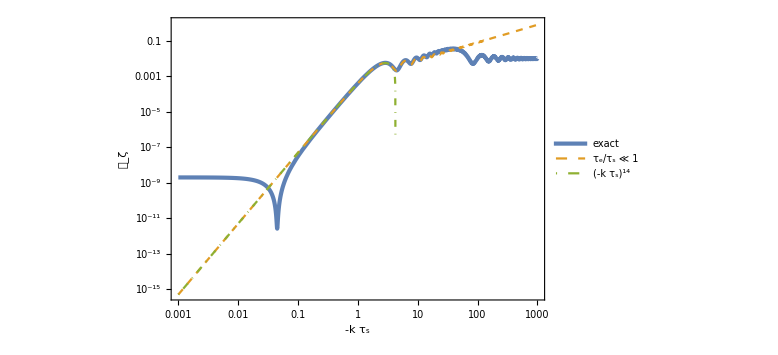

```mathematica
βs=-5/2;
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->βs};
LogLogPlot[{Abs[sqrtcalPζSR2[xs,βs,10^-lndt]]^2/.{ϵSR->10^-2,H->Hs},calPfLO[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs},calPfLOxs14[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs}},{xs,10^-3,10^3},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed,DotDashed},FrameLabel->{{Subscript[𝒫, ζ],None},{-k Subscript[τ, "s"],β==βs}},GridLines->{{4},None},PlotLegends->Placed[LineLegend[{"exact",Row[{Subscript[τ, "e"]/Subscript[τ, "s"]," ≪ ",1}],Superscript[Row[{"(",-k Subscript[τ, "s"],")"}],14]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.3}],ImagePadding->pad]
```

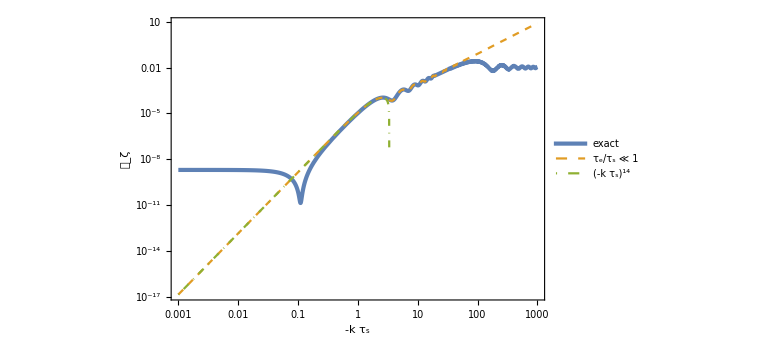

```mathematica
βs=-4/2;
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->βs};
LogLogPlot[{Abs[sqrtcalPζSR2[xs,βs,10^-lndt]]^2/.{ϵSR->10^-2,H->Hs},calPfLO[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs},calPfLOxs14[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs}},{xs,10^-3,10^3},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed,DotDashed},FrameLabel->{{Subscript[𝒫, ζ],None},{-k Subscript[τ, "s"],β==βs}},GridLines->{{4},None},PlotLegends->Placed[LineLegend[{"exact",Row[{Subscript[τ, "e"]/Subscript[τ, "s"]," ≪ ",1}],Superscript[Row[{"(",-k Subscript[τ, "s"],")"}],14]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.3}],ImagePadding->pad]
```

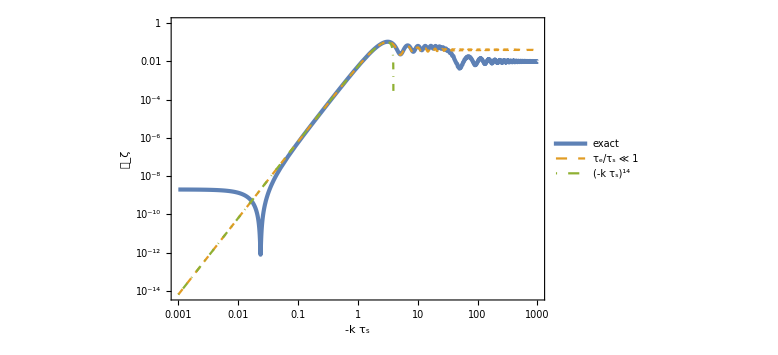

```mathematica
βs=-3;
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->βs};
LogLogPlot[{Abs[sqrtcalPζSR2[xs,βs,10^-lndt]]^2/.{ϵSR->10^-2,H->Hs},calPfLO[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs},calPfLOxs14[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs}},{xs,10^-3,10^3},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed,DotDashed},FrameLabel->{{Subscript[𝒫, ζ],None},{-k Subscript[τ, "s"],β==βs}},GridLines->{{4},None},PlotLegends->Placed[LineLegend[{"exact",Row[{Subscript[τ, "e"]/Subscript[τ, "s"]," ≪ ",1}],Superscript[Row[{"(",-k Subscript[τ, "s"],")"}],14]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.3}],ImagePadding->pad]
```

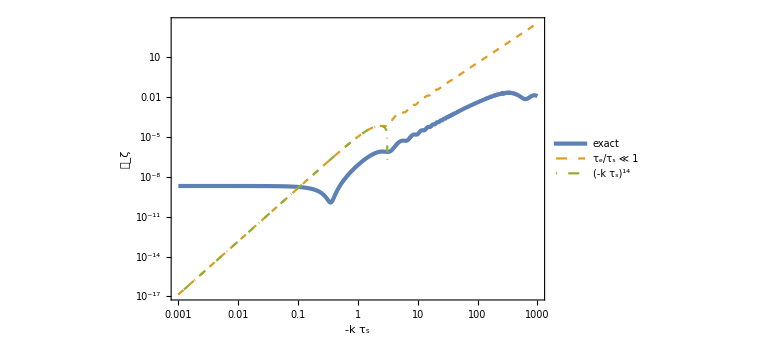

```mathematica
βs=-1.51;
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->βs};
LogLogPlot[{Abs[sqrtcalPζSR2[xs,βs,10^-lndt]]^2/.{ϵSR->10^-2,H->Hs},calPfLO[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs},calPfLOxs14[xs,βs,10^-lndt]/.{ϵSR->10^-2,H->Hs}},{xs,10^-3,10^3},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed,DotDashed},FrameLabel->{{Subscript[𝒫, ζ],None},{-k Subscript[τ, "s"],β==βs}},GridLines->{{4},None},PlotLegends->Placed[LineLegend[{"exact",Row[{Subscript[τ, "e"]/Subscript[τ, "s"]," ≪ ",1}],Superscript[Row[{"(",-k Subscript[τ, "s"],")"}],14]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.3}],ImagePadding->pad]
```

### Unify

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,H>0,k>0,xe>0,xs>0,β<0,1>f>0};
```

```mathematica
ζkSR1form1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1form2[τ_,k_]=(-I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(I k τ)(1-I k τ);
ζkSR1formp1[τ_,k_]=D[ζkSR1form1[τ,k], τ]//Simplify
ζkSR1formp2[τ_,k_]=D[ζkSR1form2[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSR1[τ_,k_]={{ζkSR1form1[τ,k]},{ζkSR1formp1[τ,k]}};
```

```mathematica
MSR1[τ_,k_]={{ζkSR1form1[τ,k],ζkSR1form2[τ,k]},{ζkSR1formp1[τ,k],ζkSR1formp2[τ,k]}};
```

```mathematica
ζkCRform1[τ_,k_,β_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-β Sqrt[-k τ]HankelH1[Abs[3/2+β],-k τ];
ζkCRformp1[τ_,k_,β_]=D[ζkCRform1[τ,k,β], τ]//Simplify
ζkCRform2[τ_,k_,β_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-β Sqrt[-k τ]HankelH2[Abs[3/2+β],-k τ];
ζkCRformp2[τ_,k_,β_]=D[ζkCRform2[τ,k,β], τ]//Simplify
```

-(H k τ (τs/τ)^-β (k τ HankelH1[-1+Abs[3/2+β],-k τ]-(3+2 β) HankelH1[Abs[3/2+β],-k τ]-k τ HankelH1[1+Abs[3/2+β],-k τ]))/(2 √2 √(-k ϵSR τ))

-(H k τ (τs/τ)^-β (k τ HankelH2[-1+Abs[3/2+β],-k τ]-(3+2 β) HankelH2[Abs[3/2+β],-k τ]-k τ HankelH2[1+Abs[3/2+β],-k τ]))/(2 √2 √(-k ϵSR τ))

```mathematica
MCR[τ_,k_,β_]={{ζkCRform1[τ,k,β],ζkCRform2[τ,k,β]},{ζkCRformp1[τ,k,β],ζkCRformp2[τ,k,β]}};
```

```mathematica
ζkSR2form1[τ_,k_,β_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-β 1/k^(3/2)E^(-I k τ)(1+I k τ)//Simplify;
ζkSR2formp1[τ_,k_,β_]=D[ζkSR2form1[τ,k,β], τ]//Simplify
ζkSR2form2[τ_,k_,β_]=(-I H)/(2Sqrt[ϵSR])(τs/τe)^-β 1/k^(3/2)E^(I k τ)(1-I k τ)//Simplify;
ζkSR2formp2[τ_,k_,β_]=D[ζkSR2form2[τ,k,β], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ (τs/τe)^-β

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ (τs/τe)^-β

```mathematica
MSR2[τ_,k_,β_]={{ζkSR2form1[τ,k,β],ζkSR2form2[τ,k,β]},{ζkSR2formp1[τ,k,β],ζkSR2formp2[τ,k,β]}};
```

```mathematica
ζkSR2[k_,β_]=Normal[Series[MSR2[τ,k,β].Inverse[MSR2[τe,k,β]].MCR[τe,k,β].Inverse[MCR[τs,k,β]].ζkSR1[τs,k],{τ,0,0}]][[1,1]];
```

```mathematica
sqrtcalPζSR2[xs_,β_,f_]=k^(3/2)/(Sqrt[2]π)ζkSR2[k,β]/.{k->-xs/τs,τe->f τs}//Simplify;
```

```mathematica
calP14th52[xs_,f_]=Normal[Series[Normal[Series[sqrtcalPζSR2[xs,-5/2,f],{xs,0,14}]]Conjugate[Normal[Series[sqrtcalPζSR2[xs,-5/2,f],{xs,0,14}]]]//FullSimplify,{xs,0,14}(*,{f,0,-4}*)]]//Simplify
```

-1/(51419848428748800 f^4 π^2 ϵSR)H^2 (702650657 f^18 xs^14-8765265720 f^16 xs^12 (2+5 xs^2)+24 f^14 xs^10 (14640470208+36601175520 xs^2+8478972395 xs^4)+400 f^12 xs^8 (-13723661952-34309154880 xs^2-9102076518 xs^4+4089579215 xs^6)-12000 f^10 xs^6 (-5341400064-13353500160 xs^2-4083319968 xs^4+1141132720 xs^6+59808349 xs^8)+15015000 xs^4 (-464486400+89800704 xs^2-7580160 xs^4+370944 xs^6-11970 xs^8+275 xs^10)-15600 f^8 xs^4 (33619525632+84048814080 xs^2+30147118848 xs^4-3477344640 xs^6-1254527886 xs^8+200091305 xs^10)+225225 f^2 xs^2 (59454259200+49545216000 xs^2+464486400 xs^4-2092253184 xs^6+274068480 xs^8-16885248 xs^10+634055 xs^12)+40040 f^6 xs^2 (66886041600+167215104000 xs^2+73820160000 xs^4+4617216000 xs^6-4534689600 xs^8+326028768 xs^10+22041115 xs^12)+20592 f^4 (-312134860800-780337152000 xs^2-502883942400 xs^4-153538560000 xs^6+34756848000 xs^8+1184831424 xs^10-590937830 xs^12+49216239 xs^14)+65520 f^2 xs^4 (3351756 f^12 xs^10-8727400 f^10 xs^8 (6+5 xs^2)-250 f^8 xs^6 (-2445696-2038080 xs^2+485461 xs^4)+4400 f^6 xs^4 (-1137024-947520 xs^2+150510 xs^4+9197 xs^6)+17325 xs^2 (3686400-712704 xs^2+60160 xs^4-2944 xs^6+95 xs^8)+440 f^4 xs^2 (58060800+48384000 xs^2-1677600 xs^4-1631184 xs^6+232865 xs^8)+2112 f^2 (-29030400-24192000 xs^2-6526800 xs^4+2239608 xs^6-236635 xs^8+13276 xs^10)) Log[f]+259459200 f^4 xs^8 (-2419200+8064 (58+125 f^2) xs^2-840 (47+232 f^2+235 f^4) xs^4+(1932+16450 f^2+38164 f^4+24125 f^6) xs^6) Log[f]^2)

```mathematica
calPf452[xs_,f_]=Abs[Normal[Series[sqrtcalPζSR2[xs,-5/2,f],{f,0,-2}]]]^2//FullSimplify
```

(25 H^2 (xs^2 BesselJ[1,xs]^2+2 xs BesselJ[1,xs] BesselJ[2,xs]+(1+xs^2) BesselJ[2,xs]^2))/(72 f^4 π^2 ϵSR)

```mathematica
calPf4xs14b52[xs_,f_]=Normal[Series[calPf452[xs,f],{xs,0,14}]]
```

(625 H^2 xs^4)/(4608 f^4 π^2 ϵSR)-(725 H^2 xs^6)/(27648 f^4 π^2 ϵSR)+(5875 H^2 xs^8)/(2654208 f^4 π^2 ϵSR)-(575 H^2 xs^10)/(5308416 f^4 π^2 ϵSR)+(2375 H^2 xs^12)/(679477248 f^4 π^2 ϵSR)-(6875 H^2 xs^14)/(85614133248 f^4 π^2 ϵSR)

```mathematica
calPf452cut[xs_,f_]=calPf452[xs,f]UnitStep[3/2 π-xs]
```

(25 H^2 (xs^2 BesselJ[1,xs]^2+2 xs BesselJ[1,xs] BesselJ[2,xs]+(1+xs^2) BesselJ[2,xs]^2) UnitStep[(3 π)/2-xs])/(72 f^4 π^2 ϵSR)

```mathematica
lndt52=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-5/2};
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

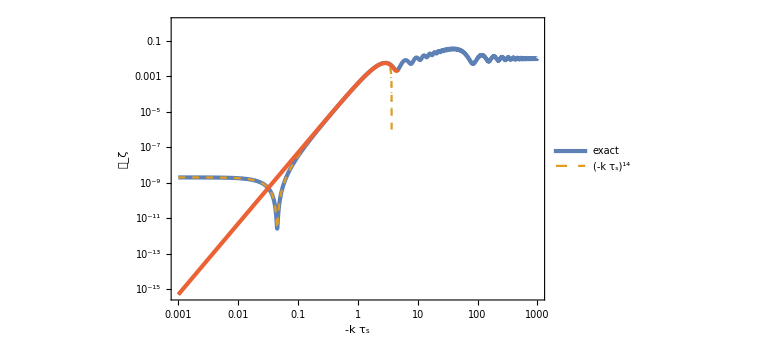

```mathematica
LogLogPlot[{Abs[sqrtcalPζSR2[k,-5/2,10^-lndt52]]^2/.{ϵSR->10^-2,H->Hs},calP14th52[k,10^-lndt52]/.{ϵSR->10^-2,H->Hs},calPf4xs14b52[k,10^-lndt52]/.{ϵSR->10^-2,H->Hs},calPf452cut[k,10^-lndt52]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,10^3},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed,Dotted},FrameLabel->{{Subscript[𝒫, ζ],None},{-k Subscript[τ, "s"],β==-"5 / 2"}},PlotLegends->Placed[{"exact",Superscript[Row[{"(",-k Subscript[τ, "s"],")"}],14]},{0.8,0.2}]]
```

```mathematica
calP14th12[xs_,f_]=Normal[Series[Normal[Series[sqrtcalPζSR2[xs,-1/2,f],{xs,0,14}]]Conjugate[Normal[Series[sqrtcalPζSR2[xs,-1/2,f],{xs,0,14}]]]//FullSimplify,{xs,0,14},{f,0,0}]]//Simplify
```

-1/(138726604800 π^2 ϵSR)H^2 (-17340825600+8670412800 xs^2-3793305600 xs^4+511795200 xs^6-36456000 xs^8+1613472 xs^10-48706 xs^12+1067 xs^14)

```mathematica
lndt12=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-1/2};
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

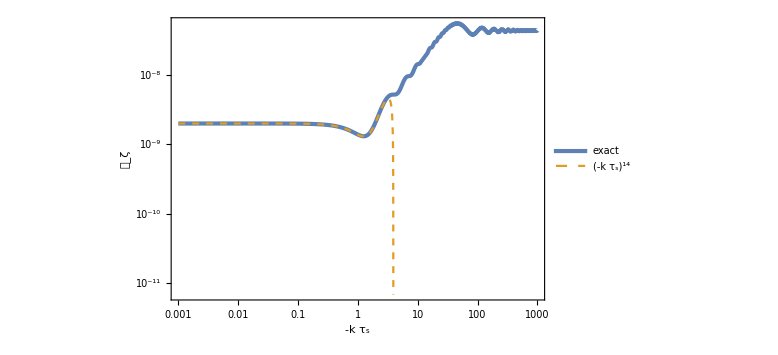

```mathematica
LogLogPlot[{Abs[sqrtcalPζSR2[k,-1/2,10^-lndt52]]^2/.{ϵSR->10^-2,H->Hs},calP14th12[k,10^-lndt52]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,10^3},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[𝒫, ζ],None},{-k Subscript[τ, "s"],β==-"1 / 2"}},PlotLegends->Placed[{"exact",Superscript[Row[{"(",-k Subscript[τ, "s"],")"}],14]},{0.8,0.2}]]
```

```mathematica
Gamma[2]
```

1

```mathematica
H10f=Normal[Series[HankelH1[Abs[3/2+β],f xs],{f,0,0}]]//Simplify
H1mf=Normal[Series[HankelH1[-1+Abs[3/2+β],f xs],{f,0,0}]]//Simplify
H1pf=Normal[Series[HankelH1[1+Abs[3/2+β],f xs],{f,0,0}]]//Simplify
H20f=Normal[Series[HankelH2[Abs[3/2+β],f xs],{f,0,0}]]//Simplify
H2mf=Normal[Series[HankelH2[-1+Abs[3/2+β],f xs],{f,0,0}]]//Simplify
H2pf=Normal[Series[HankelH2[1+Abs[3/2+β],f xs],{f,0,0}]]//Simplify
```

2^(-Abs[3/2+β]) (f xs)^(-Abs[3/2+β]) (-(ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π-(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])

(2^(1-Abs[3/2+β]) (f xs)^(-1+Abs[3/2+β]) (π+ⅈ Cos[π Abs[3/2+β]] Gamma[1-Abs[3/2+β]] Gamma[Abs[3/2+β]]))/(π Gamma[Abs[3/2+β]])

-(ⅈ 2^(1+Abs[3/2+β]) (f xs)^(-1-Abs[3/2+β]) Gamma[1+Abs[3/2+β]])/π

2^(-Abs[3/2+β]) (f xs)^(-Abs[3/2+β]) ((ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π+(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])

(2^(1-Abs[3/2+β]) (f xs)^(-1+Abs[3/2+β]) (π-ⅈ Cos[π Abs[3/2+β]] Gamma[1-Abs[3/2+β]] Gamma[Abs[3/2+β]]))/(π Gamma[Abs[3/2+β]])

(ⅈ 2^(1+Abs[3/2+β]) (f xs)^(-1-Abs[3/2+β]) Gamma[1+Abs[3/2+β]])/π

```mathematica
sqrtcalPζSR2[xs,β,f]/.{HankelH1[Abs[3/2+β],f xs]->H10f,HankelH1[-1+Abs[3/2+β],f xs]->H1mf,HankelH1[1+Abs[3/2+β],f xs]->H1pf,HankelH2[Abs[3/2+β],f xs]->H20f,HankelH2[-1+Abs[3/2+β],f xs]->H2mf,HankelH2[1+Abs[3/2+β],f xs]->H2pf}//Simplify
```

-((2^(-7/2-Abs[3/2+β]) ⅇ^(ⅈ (1+f) xs) f^(-3/2+β) H (f xs)^(-Abs[3/2+β]) (2 xs^2 ((-2 ⅇ^(-2 ⅈ f xs) (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 ((ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π+(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])-ⅈ (ⅈ+f xs+ⅇ^(-2 ⅈ f xs) (-ⅈ+f xs)) ((2 (f xs)^(2 Abs[3/2+β]) (π-ⅈ Cos[π Abs[3/2+β]] Gamma[1-Abs[3/2+β]] Gamma[Abs[3/2+β]]))/(π Gamma[Abs[3/2+β]])+(3+2 β) ((ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π+(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])-(ⅈ 2^(1+2 Abs[3/2+β]) Gamma[1+Abs[3/2+β]])/π)) HankelH1[Abs[3/2+β],xs]+ⅇ^(-2 ⅈ f xs) (2 (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 (-(ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π-(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])+(1+ⅈ f xs+ⅇ^(2 ⅈ f xs) (-1+ⅈ f xs)) ((2 (f xs)^(2 Abs[3/2+β]) (π+ⅈ Cos[π Abs[3/2+β]] Gamma[1-Abs[3/2+β]] Gamma[Abs[3/2+β]]))/(π Gamma[Abs[3/2+β]])+(3+2 β) (-(ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π-(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])+(ⅈ 2^(1+2 Abs[3/2+β]) Gamma[1+Abs[3/2+β]])/π)) HankelH2[Abs[3/2+β],xs])+(1-ⅈ xs) (ⅇ^(-2 ⅈ f xs) (2 (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 ((ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π+(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])+(1+ⅈ f xs+ⅇ^(2 ⅈ f xs) (-1+ⅈ f xs)) ((2 (f xs)^(2 Abs[3/2+β]) (π-ⅈ Cos[π Abs[3/2+β]] Gamma[1-Abs[3/2+β]] Gamma[Abs[3/2+β]]))/(π Gamma[Abs[3/2+β]])+(3+2 β) ((ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π+(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])-(ⅈ 2^(1+2 Abs[3/2+β]) Gamma[1+Abs[3/2+β]])/π)) (xs HankelH1[-1+Abs[3/2+β],xs]+(3+2 β) HankelH1[Abs[3/2+β],xs]-xs HankelH1[1+Abs[3/2+β],xs])+(-2 ⅇ^(-2 ⅈ f xs) (-1+ⅇ^(2 ⅈ f xs)) f^2 xs^2 (-(ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π-(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])-ⅈ (ⅈ+f xs+ⅇ^(-2 ⅈ f xs) (-ⅈ+f xs)) ((2 (f xs)^(2 Abs[3/2+β]) (π+ⅈ Cos[π Abs[3/2+β]] Gamma[1-Abs[3/2+β]] Gamma[Abs[3/2+β]]))/(π Gamma[Abs[3/2+β]])+(3+2 β) (-(ⅈ (f xs)^(2 Abs[3/2+β]) Cos[π Abs[3/2+β]] Gamma[-Abs[3/2+β]])/π-(ⅈ 4^Abs[3/2+β] Gamma[Abs[3/2+β]])/π+(f xs)^(2 Abs[3/2+β])/Gamma[1+Abs[3/2+β]])+(ⅈ 2^(1+2 Abs[3/2+β]) Gamma[1+Abs[3/2+β]])/π)) (xs HankelH2[-1+Abs[3/2+β],xs]+(3+2 β) HankelH2[Abs[3/2+β],xs]-xs HankelH2[1+Abs[3/2+β],xs]))))/(π xs^4 √ϵSR ((-HankelH1[-1+Abs[3/2+β],xs]+HankelH1[1+Abs[3/2+β],xs]) HankelH2[Abs[3/2+β],xs]+HankelH1[Abs[3/2+β],xs] (HankelH2[-1+Abs[3/2+β],xs]-HankelH2[1+Abs[3/2+β],xs]))))

```mathematica
calPHF14th52[xs_,f_]=Normal[Series[Normal[Series[sqrtcalPHF52[xs,f],{xs,0,14}]]Conjugate[Normal[Series[sqrtcalPHF52[xs,f],{xs,0,14}]]]//FullSimplify,{xs,0,14}]]//Simplify
```

(H^2 (-995978622880 f^18 xs^14+10127547003680 f^16 xs^12 (2+5 xs^2)-1700 f^14 xs^10 (189924127488+474810318720 xs^2+123053162185 xs^4)-20400 f^12 xs^8 (-190536338304-476340845760 xs^2-138115917990 xs^4+46991606135 xs^6)+2550 f^10 xs^6 (-13157962481664-32894906204160 xs^2-10373206896000 xs^4+2549066503360 xs^6+69926546035 xs^8)-19144125000 xs^4 (-464486400+89800704 xs^2-7580160 xs^4+370944 xs^6-11970 xs^8+275 xs^10)+63648 f^8 xs^4 (3017071411200+7542678528000 xs^2+2365617408000 xs^4-595258048000 xs^6+21095729750 xs^8+3557707399 xs^10)+95720625 f^2 xs^2 (59454259200+49545216000 xs^2-9444556800 xs^4-176504832 xs^6+112358400 xs^8-8971776 xs^10+378695 xs^12)+65345280 f^6 xs^2 (-9754214400-24385536000 xs^2-4822675200 xs^4+4278960000 xs^6-609368850 xs^8-2037117 xs^10+2685820 xs^12)+26254800 f^4 (34681651200+86704128000 xs^2-46603468800 xs^4-68339712000 xs^6+8052374400 xs^8+1016496320 xs^10-199244010 xs^12+13481873 xs^14)-12240 f^2 xs^4 (16486469400 f^12 xs^10-33079225400 f^10 xs^8 (6+5 xs^2)-325 f^8 xs^6 (-5271619584-4393016320 xs^2+983417123 xs^4)-16016 f^6 xs^4 (612230400+510192000 xs^2-115522050 xs^4+1714003 xs^6)-39414375 xs^2 (3686400-712704 xs^2+60160 xs^4-2944 xs^6+95 xs^8)-420420 f^4 xs^2 (-77414400-64512000 xs^2+25819200 xs^4-2384352 xs^6+74365 xs^8)-1201200 f^2 (38707200+32256000 xs^2-48484800 xs^4+8070048 xs^6-617750 xs^8+27969 xs^10)) Log[f]-5881075200 f^4 xs^8 (-15120000+100800 (29+105 f^2) xs^2-30 (8225+68208 f^2+106290 f^4) xs^4+(12075+172725 f^2+616482 f^4+557150 f^6) xs^6) Log[f]^2))/(65560306746654720000 f^4 π^2 ϵSR)

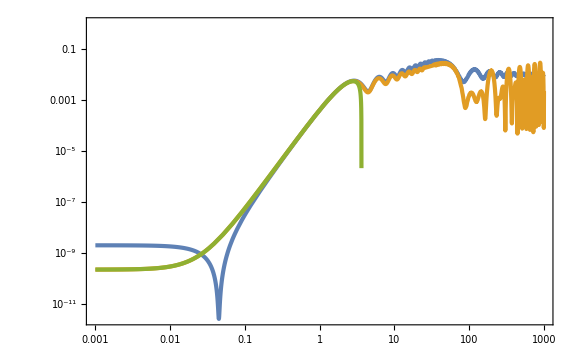

```mathematica
LogLogPlot[{Abs[sqrtcalPζSR2[k,-5/2,10^-lndt52]]^2/.{ϵSR->10^-2,H->Hs},Abs[sqrtcalPHF52[k,10^-lndt52]]^2/.{ϵSR->10^-2,H->Hs},calPHF14th52[k,10^-lndt52]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,10^3},WorkingPrecision->30]
```